```mathematica
Assuming[{rs>0,p>0},Integrate[(1/(Log[1+c]-(c/(1+c))))*(Log[1+(p*ξ/rs)]-((p*ξ/rs)/(1+p*ξ/rs)) )/((ξ^2)*(ξ^2-1)^(1/2)),ξ]]
```

((1+c) ((rs Log[rs+p ξ])/(√(-p^2+rs^2))+(√(-1+ξ^2) Log[1+(p ξ)/rs])/ξ-Log[ξ+√(-1+ξ^2)]-(rs Log[-p-rs ξ+√(-p^2+rs^2) √(-1+ξ^2)])/(√(-p^2+rs^2))))/(-c+(1+c) Log[1+c])

```mathematica
((1+c) ((rs Log[rs+p ξ])/(√(-p^2+rs^2))+(√(-1+ξ^2) Log[1+(p ξ)/rs])/ξ-Log[ξ+√(-1+ξ^2)]-(rs Log[-p-rs ξ+√(-p^2+rs^2) √(-1+ξ^2)])/(√(-p^2+rs^2))))/(-c+(1+c) Log[1+c])
```

```mathematica
F[p_,rs_,c_,ξ_]:=((1+c) ((rs Log[rs+p ξ])/(√(-p^2+rs^2))+(√(-1+ξ^2) Log[1+(p ξ)/rs])/ξ-Log[ξ+√(-1+ξ^2)]-(rs Log[-p-rs ξ+√(-p^2+rs^2) √(-1+ξ^2)])/(√(-p^2+rs^2))))/(-c+(1+c) Log[1+c])
F[p,rs,c,rs*c/p] - F[p,rs,c,1]
```

-((1+c) (-(rs Log[-p-rs])/(√(-p^2+rs^2))+(rs Log[p+rs])/(√(-p^2+rs^2))))/(-c+(1+c) Log[1+c])+1/(-c+(1+c) Log[1+c])(1+c) ((p √(-1+(c^2 rs^2)/p^2) Log[1+c])/(c rs)+(rs Log[rs+c rs])/(√(-p^2+rs^2))-Log[(c rs)/p+√(-1+(c^2 rs^2)/p^2)]-(rs Log[-p-(c rs^2)/p+√(-p^2+rs^2) √(-1+(c^2 rs^2)/p^2)])/(√(-p^2+rs^2)))

```mathematica
-((1+c) (-(rs Log[-p-rs])/(√(-p^2+rs^2))+(rs Log[p+rs])/(√(-p^2+rs^2))))/(-c+(1+c) Log[1+c])+1/(-c+(1+c) Log[1+c])(1+c) ((p √(-1+(c^2 rs^2)/p^2) Log[1+c])/(c rs)+(rs Log[rs+c rs])/(√(-p^2+rs^2))-Log[(c rs)/p+√(-1+(c^2 rs^2)/p^2)]-(rs Log[-p-(c rs^2)/p+√(-p^2+rs^2) √(-1+(c^2 rs^2)/p^2)])/(√(-p^2+rs^2)))
```

```mathematica
Assuming[{rs>0,p>0},Integrate[1/((ξ^2)*(ξ^2-1)^(1/2)),ξ]]
```

```mathematica
(√(-1+ξ^2))/ξ
G[ξ_] :=(√(-1+ξ^2))/ξ
```

(√(-1+ξ^2))/ξ

```mathematica
(√(-1+ξ^2))/ξ
Assuming[{rs>0,p>0},1 - G[rs*c/p] + F[p,rs,c,rs*c/p] - F[p,rs,c,1]]
```

(√(-1+ξ^2))/ξ

1-(p √(-1+(c^2 rs^2)/p^2))/(c rs)-((1+c) (-(rs Log[-p-rs])/(√(-p^2+rs^2))+(rs Log[p+rs])/(√(-p^2+rs^2))))/(-c+(1+c) Log[1+c])+1/(-c+(1+c) Log[1+c])(1+c) ((p √(-1+(c^2 rs^2)/p^2) Log[1+c])/(c rs)+(rs Log[rs+c rs])/(√(-p^2+rs^2))-Log[(c rs)/p+√(-1+(c^2 rs^2)/p^2)]-(rs Log[-p-(c rs^2)/p+√(-p^2+rs^2) √(-1+(c^2 rs^2)/p^2)])/(√(-p^2+rs^2)))

```mathematica
FullSimplify[1-(p √(-1+(c^2 rs^2)/p^2))/(c rs)-((1+c) (-(rs Log[-p-rs])/(√(-p^2+rs^2))+(rs Log[p+rs])/(√(-p^2+rs^2))))/(-c+(1+c) Log[1+c])+1/(-c+(1+c) Log[1+c])(1+c) ((p √(-1+(c^2 rs^2)/p^2) Log[1+c])/(c rs)+(rs Log[rs+c rs])/(√(-p^2+rs^2))-Log[(c rs)/p+√(-1+(c^2 rs^2)/p^2)]-(rs Log[-p-(c rs^2)/p+√(-p^2+rs^2) √(-1+(c^2 rs^2)/p^2)])/(√(-p^2+rs^2)))]
```

(√(-p^2+rs^2) (-c rs+p √(-1+(c^2 rs^2)/p^2))+(1+c) rs (√(-p^2+rs^2) (Log[1+c]-Log[(c rs)/p+√(-1+(c^2 rs^2)/p^2)])+rs (Log[-p-rs]+Log[(1+c) rs]-Log[p+rs]-Log[-p-(c rs^2)/p+√(-p^2+rs^2) √(-1+(c^2 rs^2)/p^2)])))/(rs √(-p^2+rs^2) (-c+(1+c) Log[1+c]))

```mathematica
U4[p_,rs_,c_]:=Piecewise[{{(√(-p^2+rs^2) (-c rs+p √(-1+(c^2 rs^2)/p^2))+(1+c) rs (√(-p^2+rs^2) (Log[1+c]-Log[(c rs)/p+√(-1+(c^2 rs^2)/p^2)])+rs (Log[-p-rs]+Log[(1+c) rs]-Log[p+rs]-Log[-p-(c rs^2)/p+√(-p^2+rs^2) √(-1+(c^2 rs^2)/p^2)])))/(rs √(-p^2+rs^2) (-c+(1+c) Log[1+c])),p/rs<c},{1, p/rs > c}}]
```

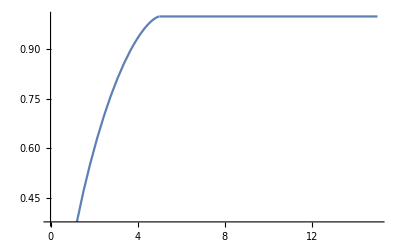

```mathematica
Plot[U4[p,1,5],{p,0,15}]
```

```mathematica
U[p_,rs_,c_] := Assuming[{p>0,rs>0,c>0},(((-c*rs+p*Sqrt[-1+(c*rs/p)^2])+(1+c)*rs*(((Log[1+c]-Log[c*rs/p+Sqrt[-1+(c*rs/p)^2]]))+(rs*(Log[(1+c)*rs]-Log[(p+c*(rs^2)/p-Sqrt[-p^2+rs^2]*Sqrt[-1+(c*rs/p)^2])])/Sqrt[-(p^2)+rs^2])))/(rs*(-c+(1+c)*Log[1+c])))]
```

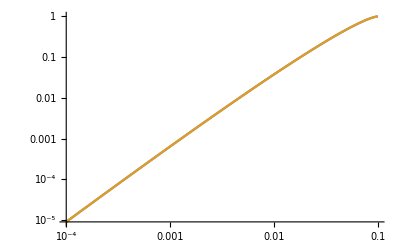

```mathematica
LogLogPlot[{U[p,1,0.1],U4[p,1,0.1]},{p,0.0001,0.1}]
```

```mathematica
Series[U[p,rs,c],{p,0,1}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

(-c rs √(rs^2)+p √(rs^2) √((c^2 rs^2)/p^2)+rs √(rs^2) Log[1+c]+c rs √(rs^2) Log[1+c]+rs^2 Log[(1+c) rs]+c rs^2 Log[(1+c) rs]-rs √(rs^2) Log[(c rs+p √((c^2 rs^2)/p^2))/p]-c rs √(rs^2) Log[(c rs+p √((c^2 rs^2)/p^2))/p]-rs^2 Log[(c rs^2-p √(rs^2) √((c^2 rs^2)/p^2))/p]-c rs^2 Log[(c rs^2-p √(rs^2) √((c^2 rs^2)/p^2))/p])/(rs √(rs^2) (-c+Log[1+c]+c Log[1+c]))+O[p]^2

```mathematica
Assuming[{c>0,rs>0,p>0},FullSimplify[(-c rs √(rs^2)+p √(rs^2) √((c^2 rs^2)/p^2)+rs √(rs^2) Log[1+c]+c rs √(rs^2) Log[1+c]+rs^2 Log[(1+c) rs]+c rs^2 Log[(1+c) rs]-rs √(rs^2) Log[(c rs+p √((c^2 rs^2)/p^2))/p]-c rs √(rs^2) Log[(c rs+p √((c^2 rs^2)/p^2))/p]-rs^2 Log[(c rs^2-p √(rs^2) √((c^2 rs^2)/p^2))/p]-c rs^2 Log[(c rs^2-p √(rs^2) √((c^2 rs^2)/p^2))/p])/(rs √(rs^2) (-c+Log[1+c]+c Log[1+c]))]]
```

∞/(-c+(1+c) Log[1+c])

```mathematica
Assuming[{rs>0,c>0},D[U[p,rs,c],p]]
```

(-(c^2 rs^2)/(p^2 √(-1+(c^2 rs^2)/p^2))+√(-1+(c^2 rs^2)/p^2)+(1+c) rs (-(-(c rs)/p^2-(c^2 rs^2)/(p^3 √(-1+(c^2 rs^2)/p^2)))/((c rs)/p+√(-1+(c^2 rs^2)/p^2))-(rs (1-(c rs^2)/p^2+(c^2 rs^2 √(-p^2+rs^2))/(p^3 √(-1+(c^2 rs^2)/p^2))+(p √(-1+(c^2 rs^2)/p^2))/(√(-p^2+rs^2))))/(√(-p^2+rs^2) (p+(c rs^2)/p-√(-p^2+rs^2) √(-1+(c^2 rs^2)/p^2)))+(p rs (Log[(1+c) rs]-Log[p+(c rs^2)/p-√(-p^2+rs^2) √(-1+(c^2 rs^2)/p^2)]))/((-p^2+rs^2)^(3/2))))/(rs (-c+(1+c) Log[1+c]))

```mathematica
Assuming[{rs>0,c>0,p>0},Limit[U[p,rs,c],p->0]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

```mathematica
LimitFct[p_,rs_,c_]:= Assuming[{p>0,rs>0,c>0},(-Sqrt[-p^2 + rs^2] * Log[rs*c / p + Sqrt[-1 + (c*rs/p)^2]] - rs*Log[p + c*rs^2/p - Sqrt[-p^2 + rs^2] * Sqrt[-1 + (c*rs/p)^2]])/(Sqrt[-p^2 + rs^2])]
```

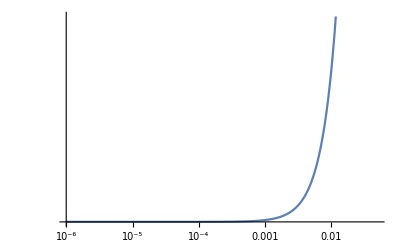

```mathematica
LogLogPlot[LimitFct[p,0.5,0.1],{p,0.000001,0.05}]
```

```mathematica
2 * Log[1+0.1] + Log[0.5]
```

-0.502527